```mathematica
solθ= DSolve[{θ''[s]+p Sin[θ[s]]==0},θ[s],{s,0,1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
solθ= DSolve[{θ''[s]+10 Sin[θ[s]]==0,θ[0]==0,θ'[1]==0},θ[s],{s,0,1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

{}

```mathematica
θtemp1 [s_]= θ[s]/.solθ[[1]]
```

-2 JacobiAmplitude[1/2 √((2 p+C[1]) (s+C[2])^2),(4 p)/(2 p+C[1])]

```mathematica
θtemp1D[s_]=D[θtemp1[s],s]
```

-((2 p+C[1]) (s+C[2]) JacobiDN[1/2 √((2 p+C[1]) (s+C[2])^2),(4 p)/(2 p+C[1])])/(√((2 p+C[1]) (s+C[2])^2))

```mathematica
Block[{p=10},
NSolve[{θtemp1[0]==0,θtemp1D[1]==0},{C[1],C[2]}]
]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{-2 JacobiAmplitude[1/2 √((20+C[1]) C[2]^2),40/(20+C[1])]==0,-((20+C[1]) (1+C[2]) JacobiDN[1/2 √((20+C[1]) (1+C[2])^2),40/(20+C[1])])/(√((20+C[1]) (1+C[2])^2))==0},{C[1],C[2]}]

```mathematica
Solve[θtemp1[0]==0,C[1]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-2 JacobiAmplitude[1/2 √((2 p+C[1]) C[2]^2),(4 p)/(2 p+C[1])]==0,C[1]]

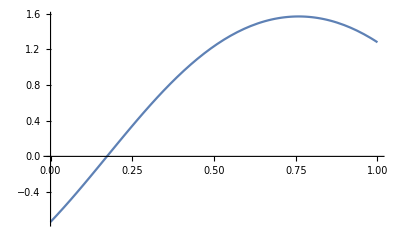

```mathematica
Block[{p=10},
Plot[-2 JacobiAmplitude[1/2 √((2 p+C[1]) (s+C[2])^2),(4 p)/(2 p+C[1])]/.{C[1]->0,C[2]->1},{s,0,1}]
]
```

```mathematica
θ[s_]=2 ArcSin[Sqrt[kn] JacobiSN[s Sqrt[p]+EllipticK[kn],kn]]
```

2 ArcSin[√kn JacobiCD[√p s,kn]]

```mathematica
D[θ[s],{s,2}]//FullSimplify
```

-(2 (-1+kn)^2 √kn p JacobiCN[√p s,kn])/((1-kn JacobiCD[√p s,kn]^2)^(3/2) JacobiDN[√p s,kn]^5)

```mathematica
Sin[θ[s]]//FullSimplify
```

Sin[2 ArcSin[√kn JacobiCD[√p s,kn]]]

0.0199853

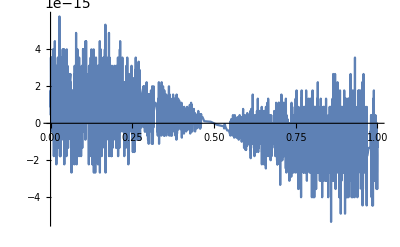

```mathematica
Module[{p= π^2+0.1,solk,kn,θ,θ2,soly,solx},
solk =FindRoot[EllipticK[x]-Sqrt[p]/2,{x,0.1}];
kn =x/.solk;
Print[kn];
LeftE[s_]=-(2 (-1+kn)^2 √kn p JacobiCN[√p s,kn])/((1-kn JacobiCD[√p s,kn]^2)^(3/2) JacobiDN[√p s,kn]^5);
RightE[s_]=- p Sin[2 ArcSin[√kn JacobiCD[√p s,kn]]];
(*RightE[s_]=-p Cos[2 ArcSin[kn JacobiCD[√p s,kn]]];*)
Plot[LeftE[s]-RightE[s],{s,0,1}]
]
```

```mathematica
PAna[P_]:=Reap@Module[{solk,kn,θ,θ2,soly,solx},
solk =FindRoot[EllipticK[x] - Sqrt[P]/2,{x,0.1}];
kn =x/.solk;
θ[s_]=2ArcSin[Sqrt[kn] JacobiSN[s Sqrt[P]+EllipticK[kn],kn]];
solx =NDSolve[{x'[s]==Cos[θ[s]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin[θ[s]],y[0]==0},y[s],{s,0,1}];
dflection = y[s]/.soly[[1]]/.s->1/2;
Sow[dflection];
ParametricPlot[{x[s]/.solx[[1]],y[s]/.soly[[1]]},{s,0,1},PlotRange->All,PlotStyle->{Dashed},ImageSize->Large]
]
```

```mathematica
π^2//N
```

9.8696

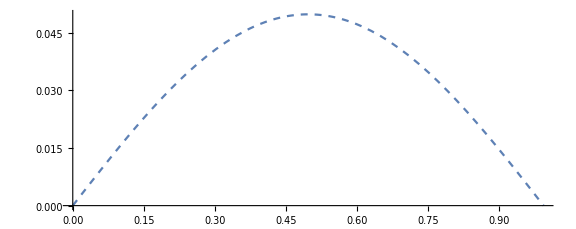
{-Graphics-,{{0.0497811}}}

```mathematica
PAna[9.9]
```

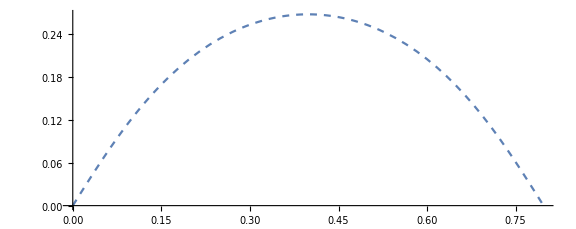
{-Graphics-,{{0.267918}}}

```mathematica
PAna[11]
```

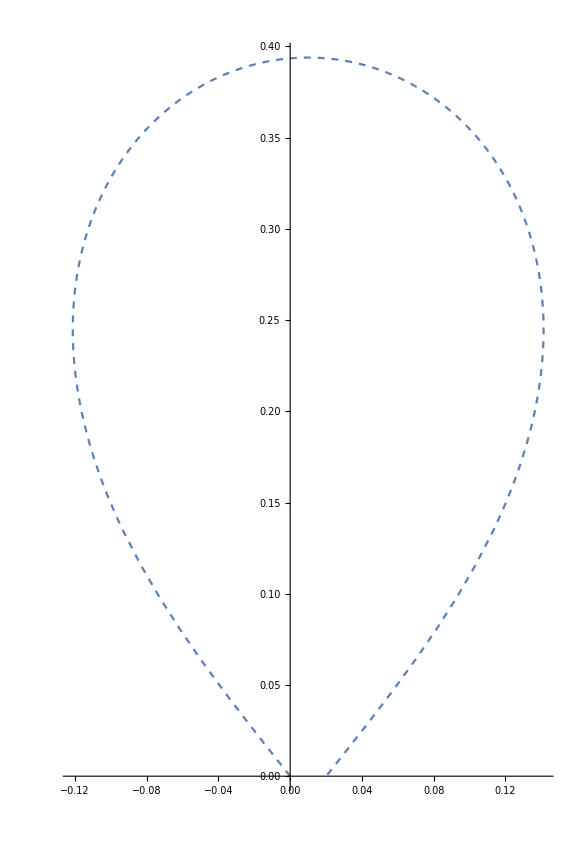
{-Graphics-,{{0.393863}}}

```mathematica
PAna[21]
```

```mathematica
Clear[P]
```

```mathematica
PShape[P_]:=Reap@Module[{solk,kn,soly,solx},
solk =FindRoot[EllipticK[k]-Sqrt[P]/2,{k,0.1}];
kn =k/.solk;
θ[s_]=2ArcSin[Sqrt[kn] JacobiSN[s Sqrt[P]+EllipticK[kn],kn]];
(*solx =NDSolve[{x'[s]==Cos[θ[s]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin[θ[s]],y[0]==0},y[s],{s,0,1}];
*)
x[s_]=-s+2/Sqrt[P](EllipticE[JacobiAmplitude[s Sqrt[P]+EllipticK[kn],kn],kn]-EllipticE[JacobiAmplitude[EllipticK[kn],kn],kn]);
y[s_]=-2 Sqrt[kn]/Sqrt[P] JacobiCN[s Sqrt[P]+EllipticK[kn],kn];
dflection = y[s]/.s->1/2;
Sow[dflection];
ParametricPlot[{Chop[x[s],10^-6],y[s]},{s,0,1},PlotRange->All,PlotStyle->{Dashed},ImageSize->Large]
]
```

```mathematica
PShape[11]
```

{-Graphics-,{{0.267918}}}

```mathematica
ClearAll[θ,x,y]
```

```mathematica
MMSFull[P0_]:=Reap@Module[{P = P0,solMM,MMθ2,solx,soly,dflection},
solMM=NDSolve[{θ''[s]+P Sin[θ[s]]==0,θ'[0]==0,θ'[1]==0},θ[s],{s,0,1}];
solx =NDSolve[{x'[s]==Cos[θ[s]/.solMM[[1]]],x[0]==0},x[s],{s,0,1}];
soly= NDSolve[{y'[s]==Sin[θ[s]/.solMM[[1]]],y[0]==0},y[s],{s,0,1}];
dflection = y[s]/.soly[[1]]/.s->1/2;
Sow[dflection];
ParametricPlot[{x[s]/.solx[[1]],y[s]/.soly[[1]]},{s,0,1},PlotRange->All,PlotStyle->{Dashed,ColorData[2][1],Thickness[0.003]},ImageSize->Large]
]
```

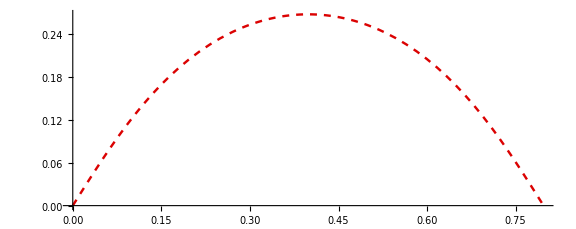
{-Graphics-,{{0.267918}}}

```mathematica
MMSFull[11]
```

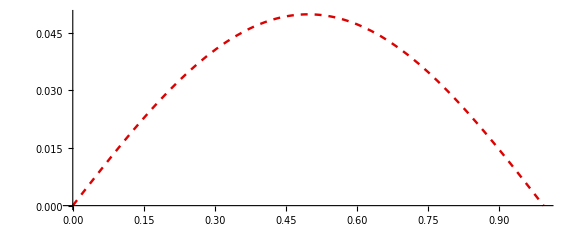
{-Graphics-,{{0.0497807}}}

```mathematica
MMSFull[9.9]
```